```mathematica
(* This code is designed for 2-dimensional lattice *)
Clear[a,b,HexagonalLattice,OrthoganolLattice,ReciprocalLattice,BasisVector]
a=1;
b=√3;

HexagonalLattice[a_]:=
{{a,0,0},{-a/2,√3*a/2,0}};
HexagonalLattice[a]
```

{{1,0,0},{-1/2,(√3)/2,0}}

```mathematica
OrthoganolLattice[a_,b_]:=
{{a,0,0},{0,b,0}};
OrthoganolLattice[a,b]
```

{{1,0,0},{0,√3,0}}

```mathematica
ReciprocalLattice[a1_,a2_]:=
{2*Pi*Cross[a2,{0,0,1}]/Dot[a1,Cross[a2,{0,0,1}]],2*Pi*Cross[{0,0,1},a1]/Dot[a2,Cross[{0,0,1},a1]]};
ReciprocalLattice[HexagonalLattice[a][[1]],HexagonalLattice[a][[2]]]
```

{{2 π,(2 π)/(√3),0},{0,(4 π)/(√3),0}}

```mathematica
ReciprocalLattice[OrthoganolLattice[a,b][[1]],OrthoganolLattice[a,b][[2]]]
```

{{2 π,0,0},{0,(2 π)/(√3),0}}

```mathematica
{ahex1,ahex2}={{HexagonalLattice[a][[1]][[1]],HexagonalLattice[a][[1]][[2]]},{HexagonalLattice[a][[2]][[1]],HexagonalLattice[a][[2]][[2]]}}
{aort1,aort2}={{OrthoganolLattice[a,b][[1]][[1]],OrthoganolLattice[a,b][[1]][[2]]},{OrthoganolLattice[a,b][[2]][[1]],OrthoganolLattice[a,b][[2]][[2]]}}
```

{{1,0},{-1/2,(√3)/2}}

{{1,0},{0,√3}}

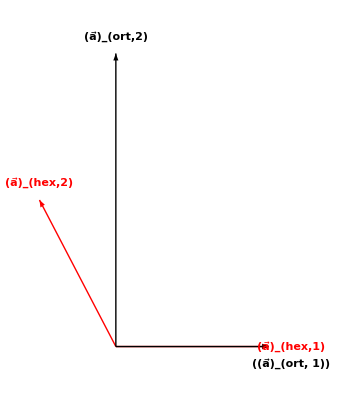

```mathematica
BasisVector[origin_,Xdirection_,Ydirection_,labels_,labelposition_,labelstyle_]:=
{Arrow[{origin,Xdirection}],Arrow[{origin,Ydirection}],
Text[Style[labels[[1]],Bold,FontFamily->"ItalicT"],labelposition[[1]]],Text[Style[labels[[2]],Bold,FontFamily->"ItalicT"],labelposition[[2]]],labelstyle};
Graphics[{{(*Direct lattice of 2D hexagonal system*)
Red,BasisVector[{0,0},ahex1,ahex2,{Subscript[OverVector["a"],hex,1],Subscript[OverVector["a"],hex,2]},{ahex1+{0.15,0},ahex2+{0,0.1}},Darker@Orange]},

{(*Direct lattice of 2D orthogonal system*)
Black,BasisVector[{0,0},aort1,aort2,{"((a⃗)_(ort, 1))",Subscript[OverVector["a"],ort,2]},{aort1+{0.15,-0.1},aort2+{0,0.1}},Darker@Orange]}},
Boxed->False]
```

```mathematica
RecHex=ReciprocalLattice[HexagonalLattice[a][[1]],HexagonalLattice[a][[2]]]
RecOrt=ReciprocalLattice[OrthoganolLattice[a,b][[1]],OrthoganolLattice[a,b][[2]]]
{bhex1,bhex2}={{RecHex[[1]][[1]],RecHex[[1]][[2]]},{RecHex[[2]][[1]],RecHex[[2]][[2]]}}
{bort1,bort2}={{RecOrt[[1]][[1]],RecOrt[[1]][[2]]},{RecOrt[[2]][[1]],RecOrt[[2]][[2]]}}
```

{{2 π,(2 π)/(√3),0},{0,(4 π)/(√3),0}}

{{2 π,0,0},{0,(2 π)/(√3),0}}

{{2 π,(2 π)/(√3)},{0,(4 π)/(√3)}}

{{2 π,0},{0,(2 π)/(√3)}}

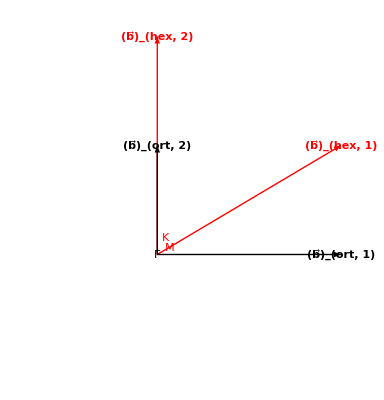

```mathematica
BrillouinZone[nodeset_]:=
{Polygon[nodeset]};
Graphics[{{(*Reciprocal lattice of 2D hexagonal system*)
Red,BasisVector[{0,0},bhex1,bhex2,{"(b⃗)_(hex, 1)","(b⃗)_(hex, 2)"},{bhex1,bhex2},Darker@Orange]},
{(*First Brillouin zone of 2D hexagonal system*)
EdgeForm[Red],Opacity[0],BrillouinZone[Table[{4*Pi*Cos[2*Pi*k/6]/3,4*Pi*Sin[2*Pi*k/6]/3},{k,6}]]},
{(*Reciprocal lattice of 2D orthogonal system*)
Black,BasisVector[{0,0},bort1,bort2,{"(b⃗)_(ort, 1)","(b⃗)_(ort, 2)"},{bort1,bort2},Darker@Orange]},
{(*First Brillouin zone of 2D orthogonal system*)
EdgeForm[Black],Opacity[0],BrillouinZone[{{bort1[[1]]/2,bort2[[2]]/2},{bort1[[1]]/2,-bort2[[2]]/2},{-bort1[[1]]/2,-bort2[[2]]/2},{-bort1[[1]]/2,bort2[[2]]/2}}]}},
Epilog->{(*Gamma*)Text[Style[Γ,FontFamily->"Times New Roman"],{-0.02,-0.02}],
(*M in hexagonal*)Text[Style[M,Red,FontFamily->"Times New Roman"],{√3/4-0.02,1/4-0.05}],
(*K in hexagonal*)Text[Style[K,Red,FontFamily->"Times New Roman"],{√3/6,1/2+0.05}]},
Boxed->False]
```